## Lossless T-Line Extension Model

```mathematica
-Graphics--Graphics-
```

```mathematica
EqnMatrix={{(ⅈ ω LL/2+1/(ⅈ ω CL)),-1/(ⅈ ω CL),0,0,0},{-1/(ⅈ ω CL),(2/(ⅈ ω CL)+ⅈ ω LL),-1/(ⅈ ω CL),0,ⅈ ω Mc},{0,-1/(ⅈ ω CL),(2/(ⅈ ω CL)+ⅈ ω LL),1/(ⅈ ω CL),ⅈ ω Mc-ⅈ ω ML},{0,0,1/(ⅈ ω CL),(ⅈ ω LL/2+1/(ⅈ ω CL)),0},{0,ⅈ ω Mc,-(ⅈ ω Mc -ⅈ ω ML),0,(RR+ⅈ ω LR+1/(ⅈ ω CR))}};
VVector={vi,0,0,vo,0};
Ans=FullSimplify[LinearSolve[EqnMatrix,VVector]/.{Mc-> kc (CR CL)^(1/2),ML-> kL (LR LL)^(1/2)}];
```

```mathematica
FullSimplify[FullSimplify[(i3/(ⅈ ω CL)+i4(ⅈ ω LL/2+1/(ⅈ ω CL)))/i1/.{i1->Ans[[2]],i2->0,i3->Ans[[3]],i4->Ans[[4]]}/.{vo->1,vi->1}]]
```

(-8 ⅈ CR √(CL CR) kc kL √(LL LR) ω^2-ⅈ CL^3 LL^4 ω^6 (-1+CR ω (-ⅈ RR+(1+kL^2) LR ω))+4 LL (-3 ⅈ+CR ω (3 RR+ⅈ (3+kL^2) LR ω+5 ⅈ CL √(CL CR) kc kL √(LL LR) ω^3))-ⅈ CL LL^2 ω^2 (-19+CR ω (-19 ⅈ RR+(19+10 kL^2) LR ω+12 CL √(CL CR) kc kL √(LL LR) ω^3))+2 CL^2 LL^3 ω^4 (-4 ⅈ+CR ω (4 RR+ⅈ ((4+3 kL^2) LR ω+CL √(CL CR) kc kL √(LL LR) ω^3))))/(2 CL ω (2 CR kc (-2 CL CR kc+3 √(CL CR) kL √(LL LR)) ω^2+CL LL^2 ω^2 (-1+CR ω (-ⅈ RR+(1+kL^2) LR ω))+LL (3+CR ω (3 ⅈ RR-(3+2 kL^2) LR ω+CL kc (2 CL CR kc-3 √(CL CR) kL √(LL LR)) ω^3))))

#### [i1, i2, i3, i4, i5] [ii, i1, i2, io, i3]

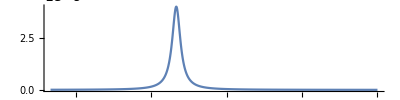

```mathematica
Z21a[CL_,LL_,RR_,LR_,CR_,kc_,kL_,ω_]:=(-8 ⅈ CR √(CL CR) kc kL √(LL LR) ω^2-ⅈ CL^3 LL^4 ω^6 (-1+CR ω (-ⅈ RR+(1+kL^2) LR ω))+4 LL (-3 ⅈ+CR ω (3 RR+ⅈ (3+kL^2) LR ω+5 ⅈ CL √(CL CR) kc kL √(LL LR) ω^3))-ⅈ CL LL^2 ω^2 (-19+CR ω (-19 ⅈ RR+(19+10 kL^2) LR ω+12 CL √(CL CR) kc kL √(LL LR) ω^3))+2 CL^2 LL^3 ω^4 (-4 ⅈ+CR ω (4 RR+ⅈ ((4+3 kL^2) LR ω+CL √(CL CR) kc kL √(LL LR) ω^3))))/(2 CL ω (2 CR kc (-2 CL CR kc+3 √(CL CR) kL √(LL LR)) ω^2+CL LL^2 ω^2 (-1+CR ω (-ⅈ RR+(1+kL^2) LR ω))+LL (3+CR ω (3 ⅈ RR-(3+2 kL^2) LR ω+CL kc (2 CL CR kc-3 √(CL CR) kL √(LL LR)) ω^3))))
χ[T1_,T2_,ωs0_,ω_,γ_]:=((T1(ωs0 -ω))/(1+T2^2(ωs0 -ω)^2+γ^2 1T1 T2)+ⅈ T1/(1+T2^2(ωs0 -ω)^2+γ^2 1T1 T2))
gL=.000025 ;
gR=.007 ;
kkc=0.01 0;
kkL=0.005 0;
Rv=.001;
T1=4 10^-9;
T2=.1 10^-9;
γ=2.8 ;
Show[Plot[Im[
χ[T1,T2,1.4 250 10^9,f,γ]
],{f,100 10^9,750 10^9},PlotRange->All,AspectRatio->1/4,PlotStyle->Automatic]
]
LR[T1_,T2_,ωs0_,ω_,γ_,Dr_,dr_,gr_]:=4π 10^-7 (1+gr χ[T1,T2,ωs0,ω,γ])Dr/2(Log[(8 Dr)/dr]-2)
lineStyle={Black,Dashed};
line1=Line[{{398 10^9,-6 10^19},{398 10^9,6 10^9}}];
line2=Line[{{440 10^9,-6 10^19},{440 10^9,6 10^9}}];
```

### Coupled Only

```mathematica
gL=  0 1000 10^-8 ;
gR=  4700 10^-8 ;
kkc=0.255 ;
kkL=0.065 ;
Rv=.0008;
output=Table[2Re[
1-(Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9 i,f,γ]),Rv, LR[T1,T2,300 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]/Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,295 10^9 i,f,γ]),Rv, LR[T1,T2,295 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f])
],{f,255 10^9,700 10^9,.5 10^9},{i,1.7,1.2,-.025}];
Export["C:/Users/sidabras/Desktop/CoupledOnly.CSV",output,"CSV"]
Clear[output]
```

### With Transmission

```mathematica
gL=1000 10^-8;
gR=4000 10^-8 ;
kkc=0.255;
kkL=0.065;
Rv=.0008;
```

```mathematica
output=Table[ 2 Re[
1-(Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9 i,f,γ]),Rv, LR[T1,T2,300 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]/Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,295 10^9 i,f,γ]),Rv, LR[T1,T2,295 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f])
],{f,255 10^9,700 10^9,0.5 10^9},{i,1.7,1.2,-.025}];
Export["~/Desktop/WithTransmission.CSV",output,"CSV"]
Clear[output]
```

### Only Transmission

```mathematica
gL=1000 10^-8 ;
gR=4000 10^-8;
kkc=0.255 0;
kkL=0.065 0;
Rv=.0008;
output=Table[2 Re[
1-(Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9 i,f,γ]),Rv, LR[T1,T2,300 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]/Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,295 10^9 i,f,γ]),Rv, LR[T1,T2,295 10^9 i,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f])
],{f,255 10^9,700 10^9,0.5 10^9},{i,1.7,1.2,-.025}];*)
(*Export["~/Desktop/OnlyTransmission.CSV",output,"CSV"]
Clear[output]
```

### Strong and Weak Coupling Studies

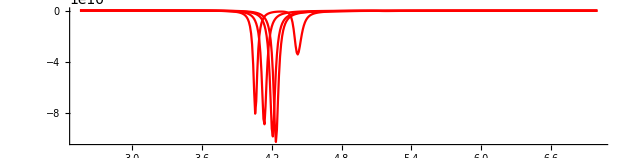

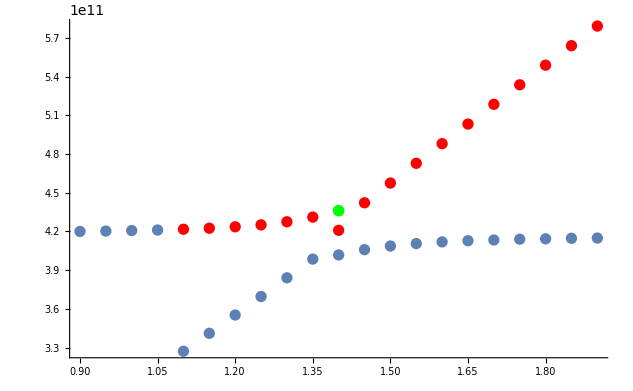

```mathematica
gL=  0 1000 10^-8 ;
gR=  100 4700 10^-8 ;
kkc=0.255 ;
kkL=0.065 ;
Rv=.0008/5;
Show[Plot[Re[
Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9#,f,γ]),Rv, LR[T1,T2,300 10^9#,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]
],{f,255 10^9,700 10^9},PlotRange->All,PlotPoints->500,MaxRecursion->0,AspectRatio->1/4,PlotStyle->Red]&/@{1.7,1.45,1.2,1},PlotRange->All]
tab1=Table[Re[
Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9#,f,γ]),Rv, LR[T1,T2,300 10^9#,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]
],{f,255 10^9,700 10^9,.1 10^9}]&/@Table[i,{i,0.9,1.9,.05}];
freq1={};
freq2={};
freq3={};
posout={};
For[i=1,i≤ Length[tab1],i++,
tlist=Table[i,{i,0.9,1.9,.05}];
pos1=FindPeaks[-tab1[[i]]];
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[1,1]]]];
AppendTo[freq1,{tlist[[i]],freq}];
If[Length[pos1]==2,
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[2,1]]]];
AppendTo[freq2,{tlist[[i]],freq}];
];
If[Length[pos1]==3,
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[2,1]]]];
AppendTo[freq2,{tlist[[i]],freq}];
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[3,1]]]];
AppendTo[freq3,{tlist[[i]],freq}];
];
If[Length[pos1]==4,
Print["you missed!"];
];
]
Show[ListPlot[freq1],
ListPlot[freq2,PlotStyle->Red],
ListPlot[freq3,PlotStyle->Green],PlotRange->All]
```

```mathematica
gL=  1 10^-8 ;
gR=  4.7 10^-8 ;
kkc=0.255 ;
kkL=0.065 ;
Rv=.0008;
Show[Plot[Re[
Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9#,f,γ]),Rv, LR[T1,T2,300 10^9#,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]
],{f,255 10^9,700 10^9},PlotRange->All,PlotPoints->500,MaxRecursion->0,AspectRatio->1/4,PlotStyle->Red]&/@{1.7,1.45,1.2,1},PlotRange->All]
tab1=Table[Re[
Z21a[8.854 10^-12,4π 10^-7 (1+gL χ[T1,T2,300 10^9#,f,γ]),Rv, LR[T1,T2,300 10^9#,f,γ,10 10^-9,0.095 10^-9,gR],  1.93 10^-10,kkc,kkL, f]
],{f,255 10^9,700 10^9,.1 10^9}]&/@Table[i,{i,0.9,1.9,.005}];
freq5={};
freq6={};
For[i=1,i≤ Length[tab1],i++,
tlist=Table[i,{i,0.9,1.9,.005}];
pos1=FindPeaks[-tab1[[i]]];
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[1,1]]]];
AppendTo[freq5,{tlist[[i]],freq}];
If[Length[pos1]==2,
freq=Table[f,{f,255 10^9,700 10^9,.1 10^9}][[pos1[[2,1]]]];
AppendTo[freq6,{tlist[[i]],freq}];
];
]
```

$Aborted

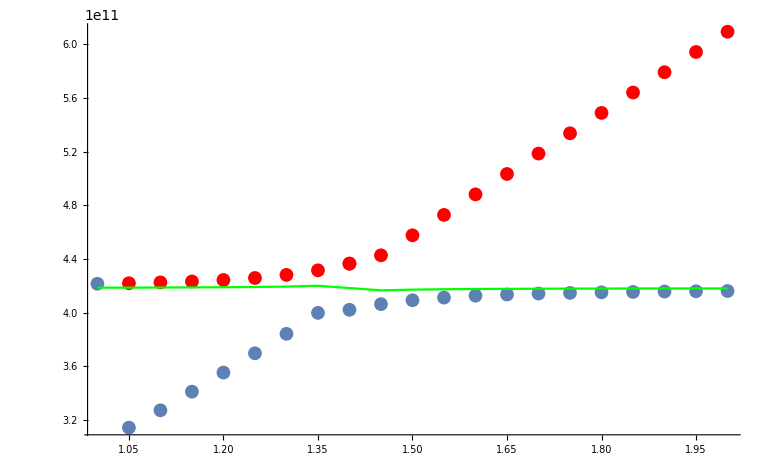

```mathematica
Show[ListPlot[freq1],
ListPlot[freq2,PlotStyle->Red],
ListPlot[freq3,PlotStyle->Red],
ListLinePlot[freq5,PlotStyle->Green],PlotRange->All]
```